```mathematica
ClearAll;
SetOptions[Plot, Filling->Axis, GridLines->Automatic, Frame->True];
```

# Define Functions

```mathematica
psi[c_,p_]:=(c*(2*p+1)*(Factorial[2*p]/(2^p *Factorial[p]))^2)/2
Hes[c_,p_,x_]:=((-1)^p/2)*(LegendreP[p,x]-((psi[c,p])*LegendreP[p-1,x]+LegendreP[p+1,x])/(psi[c,p]+1))
Hdg[p_,x_]:=((-1)^p/2)*(LegendreP[p,x]-LegendreP[p+1,x])
Hsd[p_,x_]:=((-1)^p/2)*(LegendreP[p,x]-(p*LegendreP[p-1,x]+(p+1)*LegendreP[p+1,x])/(2*p+1))
Hg2[p_,x_]:=((-1)^p/2)*(LegendreP[p,x]-((p+1)*LegendreP[p-1,x]+p*LegendreP[p+1,x])/(2*p+1))
Hgk1[p_,x_]:=((-p/(2+p))-x)/((-p/(2+p))+1)*((1-x)/2)^p
Hgk[p_,x_]:=((1-x)/2)^(p+1)
Hmax[p_,x_]:=Limit[Hes[c,p,x],c->Infinity]
Hmin[p_,x_]:=Limit[Hes[c,p,x],c->-Infinity]
```

## Plot Stuff

{{x→-1},{x→1}}

{{x→0}}

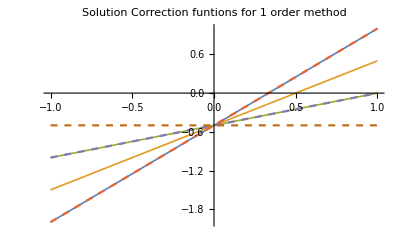

{{x→-1},{x→0},{x→1}}

{{x→-1/(√3)},{x→1/(√3)}}

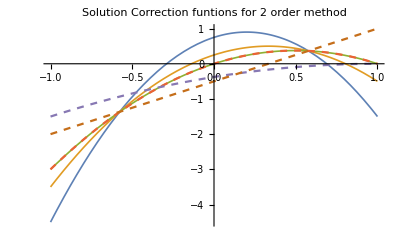

{{x→-1},{x→1},{x→-1/(√5)},{x→1/(√5)}}

{{x→0},{x→-√(3/5)},{x→√(3/5)}}

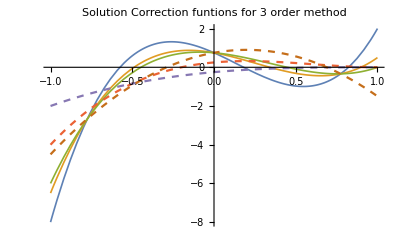

{{x→-1},{x→0},{x→1},{x→-√(3/7)},{x→√(3/7)}}

{{x→-√(1/35 (15-2 √30))},{x→√(1/35 (15-2 √30))},{x→-√(1/35 (15+2 √30))},{x→√(1/35 (15+2 √30))}}

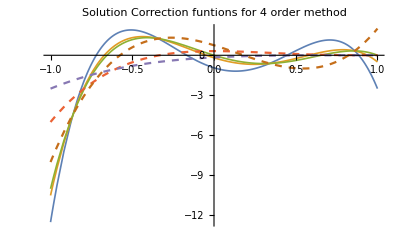

```mathematica
For[p=1,p≤4,p++,{
Solve[Hdg[p,x]==Hg2[p,x]]//Print,
Solve[D[Hdg[p,x],x]==D[Hg2[p,x],x]]//Print,

GraphicsRow[{
Plot[{Hdg[p,x],Hsd[p,x],Hg2[p,x],Hgk1[p,x],Hgk[p,x],Hmax[p,x]},{x,-1,1},PlotRange->Full,
PlotStyle->{Thickness[.003],Thickness[.003],Thickness[.003],Dashed,Dashed,Dashed},
PlotLegends->Placed["Expressions",Below],
PlotLabel->Framed[StringForm["Flux Correction funtions for `` order method",p],Background->Lighter[Yellow]],ImageSize->Scaled[0.85]],

Plot[Evaluate[D[{Hdg[p,x],Hsd[p,x],Hg2[p,x],Hgk1[p,x],Hgk[p,x],Hmax[p,x]},x]],{x,-1,1},PlotRange->Full,PlotStyle->{Thickness[.003],Thickness[.003],Thickness[.003],Dashed,Dashed,Dashed},PlotLabel->Framed[StringForm["Solution Correction funtions for `` order method",p],Background->Lighter[Yellow]],ImageSize->Full]
},ImageSize->Full]//Print
}]
```

# Some other stuff

```mathematica
Solve[LegendreP[2,x]==0]
Solve[LegendreP[3,x]==0]
Solve[LegendreP[4,x]==0]
Solve[LegendreP[5,x]==0]
```

{{x→-1/(√3)},{x→1/(√3)}}

{{x→0},{x→-√(3/5)},{x→√(3/5)}}

{{x→-√(1/35 (15-2 √30))},{x→√(1/35 (15-2 √30))},{x→-√(1/35 (15+2 √30))},{x→√(1/35 (15+2 √30))}}

{{x→0},{x→-1/3 √(1/7 (35-2 √70))},{x→1/3 √(1/7 (35-2 √70))},{x→-1/3 √(1/7 (35+2 √70))},{x→1/3 √(1/7 (35+2 √70))}}

```mathematica
Expand[D[Hdg[p,x],x]-D[Hdg[p-1,x],x]]
Expand[D[Hg2[p,x],x]-D[Hg2[p-1,x],x]]
Expand[D[Hmax[p,x],x]-D[Hmax[p-1,x],x]]
Factor[D[Hdg[p,x],x]-D[Hmax[p,x],x]]
```

(165 x)/16-(385 x^3)/8+(693 x^5)/16

-15/16+(75 x)/16+(75 x^2)/8-(175 x^3)/8-(175 x^4)/16+(315 x^5)/16

-27/16+(135 x^2)/8-(315 x^4)/16

11/16 x (15-70 x^2+63 x^4)

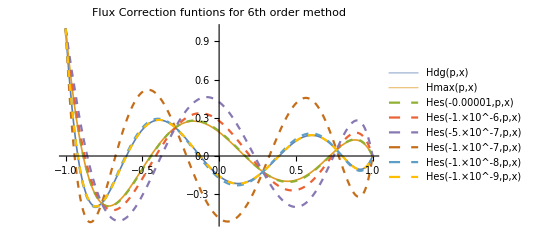

```mathematica
Plot[{Hdg[p,x],Hmax[p,x],Hes[-0.00001,p,x],Hes[-0.000001,p,x],Hes[-0.0000005,p,x],Hes[-0.0000001,p,x],Hes[-0.00000001,p,x],Hes[-0.000000001,p,x]},{x,-1,1},PlotRange->All,PlotStyle->{Thickness[.003],Thickness[.003],Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed},PlotLegends->"Expressions",PlotLabel->Framed["Flux Correction funtions for 6th order method",Background->Lighter[Yellow]],ImageSize->Full]
```

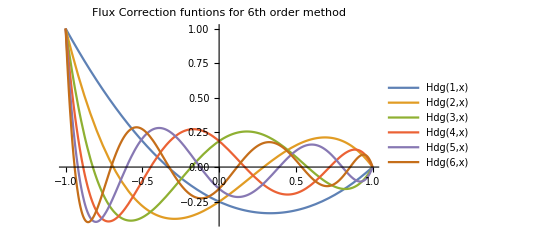

```mathematica
Plot[{Hdg[1,x],Hdg[2,x],Hdg[3,x],Hdg[4,x],Hdg[5,x],Hdg[6,x]},{x,-1,1},PlotRange->All,PlotLegends->"Expressions",PlotLabel->Framed["Flux Correction funtions for 6th order method",Background->Lighter[Yellow]],ImageSize->Full]
```